# Mathematica Notebook for Problem Set 4

## Phase portrait

- Make a stream plot.
- Add fixed points.
- Unstable manifolds (for each saddle point):
    - Compute the Jacobian matrix evaluated at that saddle point.
    - Find the unstable eigendirection.
    - Create initial conditions very close to the fixed point, with a small component of the unstable eigendirection added.
    - Create initial conditions very close to the fixed point, with a small component of the unstable eigendirection subtracted.
    - Numerically integrate from those initial conditions using the full nonlinear system.  In forwards time, trajectories approach the unstable manifold branches so if we start near them the trajectory will approximate them.
    - Cut off integration at a fixed time or when the trajectory leaves a set region.
    - Add those trajectories to the phase portrait.
- Stable manifolds (also for each saddle point):
    - Using the Jacobian from above, find the stable eigendirection.
    - Create initial conditions very close to the fixed point, with a small component of the stable eigendirection added.
    - Create initial conditions very close to the fixed point, with a small component of the stable eigendirection subtracted.
    - Numerically integrate from those initial conditions using the backwards-time version of the full nonlinear system.  In backwards time, the stable manifold branches become unstable manifold branches, and nearby trajectories will approach them.
    - Cut off integration at a fixed time or when the trajectory leaves a set region.
    - Add those trajectories to the phase portrait.

### Create the stream plot

```mathematica
f[x_,y_]={x(3-x-y),y(2-2x-y)}
```

{x (3-x-y),(2-2 x-y) y}

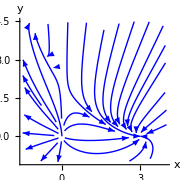

```mathematica
s1a=StreamPlot[f[x,y],{x,-1.5,4},{y,-1,4.5},Axes->True,Frame->False,AxesLabel->{x,y},LabelStyle->Medium,StreamPoints->30,StreamScale->Large,StreamStyle->{Blue,"Line"},ImageSize->Small];
p1=Normal[s1a]/. Line[x_]:>{Arrowheads[{{0.06,0.5}}],Arrow[x]}
```

### Add the fixed points and their stability information

{{x→-1,y→4},{x→0,y→2},{x→3,y→0},{x→0,y→0}}

{{3-2 x-y,-x},{-2 y,2-2 x-2 y}}

{-3,-1,-7,5}

{4,-2,12,6}

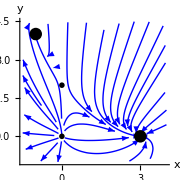

```mathematica
fixedpoints = Solve[f[x,y]==0,{x,y}]
(* find the trace and determinant and use that to determine stability *)
jacobian = Grad[f[x,y],{x,y}]
Tr[jacobian]/.fixedpoints
Det[jacobian]/.fixedpoints

markersize = 0.05;

(* stable fixed points are 1 and 3 *)
p2a = ListPlot[{x,y}/.fixedpoints[[{1,3}]],PlotStyle->{PointSize[markersize],Black}];
(* unstable fixed points are 2 and 4 *)
p2b = ListPlot[{x,y}/.fixedpoints[[{2,4}]],PlotStyle->{PointSize[markersize],Black},PlotMarkers->"OpenMarkers"];
Show[p1,p2a,p2b]
```

### Add unstable manifolds

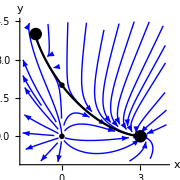

```mathematica
saddlept=fixedpoints[[2]];
saddlejac=jacobian/. saddlept;
{eigvals,eigvecs}=Eigensystem[saddlejac];

vUns=Normalize@eigvecs[[First@Ordering[Re@eigvals,-1]]];

eps=0.01;
tMax=15;

ICsp=({x,y}/. saddlept);
(* create the initial condition equations *)
icRule[sgn_]:=Thread[{x[0],y[0]}==(ICsp+sgn* eps* vUns)]; 

unstablemanifoldPlot[sgn_]:=Module[{sol},sol=NDSolve[{{x'[t],y'[t]}==f[x[t],y[t]],icRule[sgn]},{x,y},{t,0,tMax}];
(* In case the solution terminated early, get the right end time to avoid plot artifacts *)
xsoln=x/. sol[[1]];
tStop=xsoln["Domain"][[1,2]];
ParametricPlot[Evaluate@({x[t],y[t]}/. sol),{t,0,tStop},PlotStyle->{Black}]];

p3=unstablemanifoldPlot[+1];
p4=unstablemanifoldPlot[-1];

Show[p1,p2a,p2b,p3,p4]
```

### Add stable manifolds (need saddlept, eigvecs, etc from above)

{0,1}

NDSolve::ndsz: At t == 2.65165, step size is effectively zero; singularity or stiff system suspected.

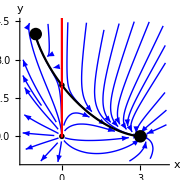

```mathematica
(* find eigenvector of smallest eigenvalue *)
vStable=Normalize@eigvecs[[First@Ordering[Re@eigvals,1]]]


eps=0.01;
tMax=15;

ICsp=({x,y}/. saddlept);
(* create the initial condition equations *)
icRuleS[sgn_]:=Thread[{x[0],y[0]}==(ICsp+sgn* eps* vStable)]; 

stablemanifoldPlot[sgn_]:=Module[{sol,xsoln,tStop},sol=NDSolve[{{x'[t],y'[t]}==-f[x[t],y[t]],icRuleS[sgn]},{x,y},{t,0,tMax}];
(* In case the solution terminated early, get the right end time to avoid plot artifacts *)
xsoln=x/. sol[[1]];
tStop=xsoln["Domain"][[1,2]];
ParametricPlot[Evaluate@({x[t],y[t]}/. sol),{t,0,tStop},PlotStyle->{Red}]];

p5=stablemanifoldPlot[+1];
p6=stablemanifoldPlot[-1];

fullplot = Show[p1,p2a,p2b,p3,p4,p5,p6]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"PSet04-phaseportraitwithmanifolds-S26.png"}],fullplot,ImageResolution->300]
```